```mathematica
Remove["Global`*"]
```

```mathematica
x0:=Sqrt[h/(m omega)]
```

```mathematica
m:=1
```

```mathematica
h:=1
```

```mathematica
omega:=1
```

```mathematica
psi[x_,t_,n_]:=1/Sqrt[x0 2^n Factorial[n]] Pi^(-1/4) HermiteH[n,x/x0]Exp[-x^2/(2x0^2)]Exp[-I(n+1/2)omega t]
```

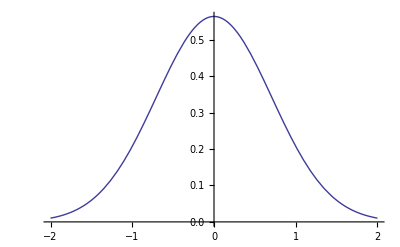

```mathematica
Plot[Abs[psi[x,0,0]]^2,{x,-2x0,2x0}]
```

```mathematica
Manipulate[Plot[Abs[psi[x,0,0]+eps1 psi[x,0,1]+eps2 psi[x,0,2]+eps3 psi[x,0,3]]^2,{x,-2x0,2x0}],{eps1,0,0.1},{eps2,0,0.1},{eps3,0,0.1}]
```

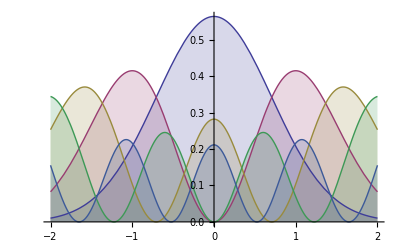

```mathematica
Plot[Evaluate[Table[Abs[psi[x,0,n]]^2,{n,0,4}]],{x,-2x0,2x0},Filling->Axis]
```

```mathematica
Manipulate[DensityPlot[Abs[psi[x,t,0]+eps1 psi[x,t,1]+eps2 psi[x,t,2]+eps3 psi[x,t,3]]^2,{x,-2x0,2x0},{t,0,10},AxesLabel->{"x", "t", "rho"}, PerformanceGoal->Quality],{eps1,0,0.1},{eps2,0,0.1},{eps3,0,0.1}]
```